NIntegrate::inumr: The integrand 0.000184835\ ⅇ^-9.07618×10^-8\ √« 1 » + « 1 »/lambda\ (ⅇ^π^2\ (1/1600000000 + thetax^2)/312500000\ lambda^2 - Cos[9.07618×10^-8\ thetay/lambda + 2\ ArcTan[Times[« 2 »]]])/lambda\ (1/1600000000 + thetax^2 + thetay^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}, {0, 0.00282799}}.

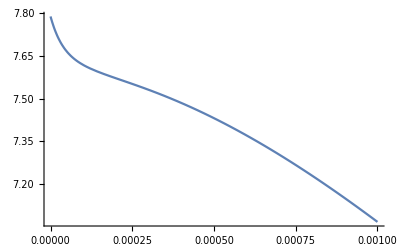

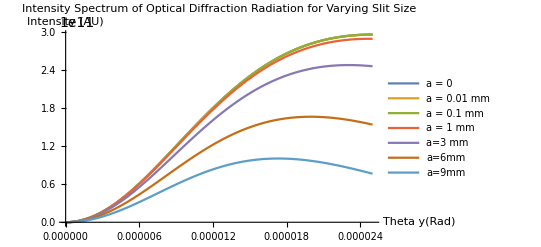

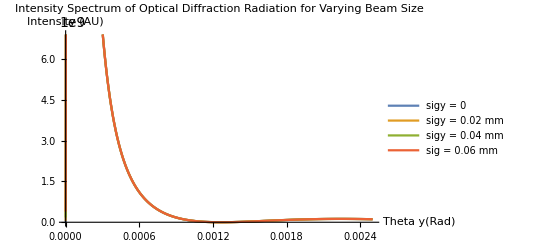

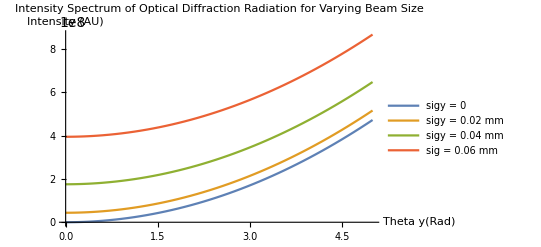

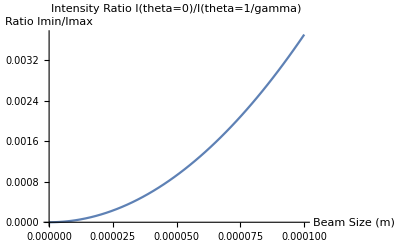

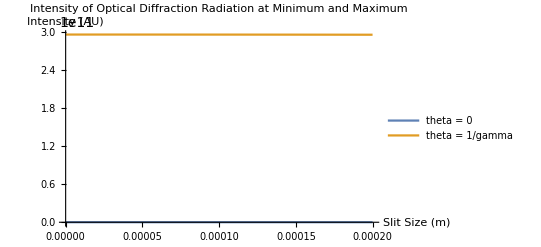

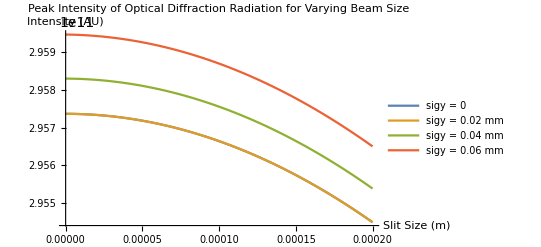

```mathematica
gamma=40000;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.00028280000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
theta0=Pi/4;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

Phi[lambda_,thetax_,thetay_]:=
ArcTan[thetay/Sqrt[1/gamma^2+thetax^2]]

Nbunch[lambda_,thetax_,thetay_,a_,sigy_]:=
alpha/(4*Pi^2)*1/lambda*Exp[-2*Pi*a*Sin[theta0]*Sqrt[1/gamma^2+thetax^2]/(lambda)]/(thetax^2+thetay^2+1/gamma^2)*(Exp[8*Pi^2*sigy^2/(lambda)^2*(1/gamma^2+thetax^2)]-Cos[2*Pi*a*Sin[theta0]*thetay/lambda+2*Phi[lambda,thetax,thetay]])

Plot[First[FindMaximum[NIntegrate[Nbunch[lambda,thetax,thetay,a,sigy],{lambda,lowerlambda,upperlambda},{thetax,-thetalens,thetalens}],{thetay,0,10/gamma}]],{a,0,0.001}]

(*NIntegrate[Nbunch[lambda,thetax,thetay,a,sigy],{lambda,lowerlambda,upperlambda},{thetax,-.05/gamma,.05/gamma},{thetay,-.05/gamma,.05/gamma}]*)

Plot[{Nbunch[averagelambda,0,thetay,0,sigy],Nbunch[averagelambda,0,thetay,10*^-6,sigy],Nbunch[averagelambda,0,thetay,100*^-6,sigy],Nbunch[averagelambda,0,thetay,1000*^-6,sigy],Nbunch[averagelambda,0,thetay,3000*^-6,sigy],Nbunch[averagelambda,0,thetay,6000*^-6,sigy],Nbunch[averagelambda,0,thetay,9000*^-6,sigy]},{thetay, 0,1/gamma},AxesLabel-> {"Theta y(Rad)","Intensity (AU)"},PlotLabel->"Intensity Spectrum of Optical Diffraction Radiation for Varying Slit Size",PlotLegends->{"a = 0","a = 0.01 mm","a = 0.1 mm","a = 1 mm","a=3 mm", "a=6mm", "a=9mm"}]

Plot[{Nbunch[averagelambda,0,thetay,a,0],Nbunch[averagelambda,0,thetay,a,20*^-6],Nbunch[averagelambda,0,thetay,a,40*^-6],Nbunch[averagelambda,0,thetay,a,60*^-6]},{thetay, 0,100/gamma},AxesLabel-> {"Theta y(Rad)","Intensity (AU)"},PlotLabel->"Intensity Spectrum of Optical Diffraction Radiation for Varying Beam Size",PlotLegends->{"sigy = 0","sigy = 0.02 mm","sigy = 0.04 mm","sig = 0.06 mm"}]

Plot[{Nbunch[averagelambda,0,thetay,a,0],Nbunch[averagelambda,0,thetay,a,20*^-6],Nbunch[averagelambda,0,thetay,a,40*^-6],Nbunch[averagelambda,0,thetay,a,60*^-6]},{thetay, 0,0.02/gamma},AxesLabel-> {"Theta y(Rad)","Intensity (AU)"},PlotLabel->"Intensity Spectrum of Optical Diffraction Radiation for Varying Beam Size",PlotLegends->{"sigy = 0","sigy = 0.02 mm","sigy = 0.04 mm","sig = 0.06 mm"}]

Plot[Nbunch[averagelambda,0,0,a,sigy]/Nbunch[averagelambda,0,1/gamma,a,sigy],{sigy, 0,100*^-6},AxesLabel-> {"Beam Size (m)","Ratio Imin/Imax"},PlotLabel->"Intensity Ratio I(theta=0)/I(theta=1/gamma)"]

Plot[{Nbunch[averagelambda,0,0,a,sigy],Nbunch[averagelambda,0,1/gamma,a,sigy]},{a,0,10*sigy},AxesLabel-> {"Slit Size (m)","Intensity (AU)"},PlotLabel->"Intensity of Optical Diffraction Radiation at Minimum and Maximum",PlotLegends->{"theta = 0","theta = 1/gamma"}]

Plot[{Nbunch[averagelambda,0,1/gamma,a,0],Nbunch[averagelambda,0,1/gamma,a,20 ^-6],Nbunch[averagelambda,0,1/gamma,a,40*^-6],Nbunch[averagelambda,0,1/gamma,a,60*^-6]},{a,0,10*sigy},AxesLabel-> {"Slit Size (m)","Intensity (AU)"},PlotLabel->"Peak Intensity of Optical Diffraction Radiation for Varying Beam Size",PlotLegends->{"sigy = 0","sigy = 0.02 mm","sigy = 0.04 mm","sigy = 0.06 mm"}]
```